```mathematica
Clear[src,outp];
src=NotebookDirectory[];
outp=src~~"output\\";

files=.
files=FileNames[All,src~~"raw-data\\"(*~~ID*),#]&/@{1,2}; (*01 entfernen*)  
pexaFiles=.
logFiles=.
respFiles=.
pexaFiles=StringCases[files[[2]],__~~".xlsx"]/.{}->Nothing;
logFiles=StringCases[files[[2]],__~~"_protocol.txt"]/.{}->Nothing;
respFiles=StringCases[files[[2]],__~~"Spiro und Diff.tsv"]/.{}->Nothing;
evalfiles=.
evalfiles=Transpose[{Flatten@pexaFiles,Flatten@logFiles,Flatten@respFiles}]
```

{{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\01\2023-03-07 10.01.47.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\01\01_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\01\QHA01 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\02\2023-03-10 09.47.59.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\02\02_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\02\QHA02 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\03\2023-03-10 12.46.27.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\03\03_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\03\QHA03 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\04\2023-03-17 16.23.29.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\04\04_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\04\QHA04 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\05\2023-03-17 18.29.59.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\05\05_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\05\QHA05 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\06\2023-03-21 09.18.10.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\06\06_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\06\QHA06 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\07\2023-03-21 13.03.53.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\07\07_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\07\QHA07 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\08\2023-03-23 09.23.06.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\08\08_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\08\QHA08 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\09\2023-03-23 13.27.18.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\09\09_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\09\QHA09 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\10\2023-03-28 13.24.24.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\10\10_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\10\QHA10 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\11\2023-03-29 09.16.03.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\11\11_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\11\QHA11 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\12\2023-03-29 13.33.25.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\12\12_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\12\QHA12 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\13\2023-04-03 08.40.54.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\13\13_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\13\QHA13 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\14\2023-04-03 10.52.04.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\14\14_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\14\QHA14 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\15\2023-04-04 15.16.01.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\15\15_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\15\QHA15 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\16\2023-04-04 17.53.08.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\16\16_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\16\QHA16 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\17\2023-04-05 10.17.32.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\17\17_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\17\QHA17 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\18\2023-04-05 12.24.27.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\18\18_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\18\QHA18 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\19\2023-04-06 10.27.28.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\19\19_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\19\QHA19 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\20\2023-04-12 09.33.55.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\20\20_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\20\QHA20 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\21\2023-04-12 12.18.05.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\21\21_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\21\QHA21 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\22\2023-04-13 13.26.25.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\22\22_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\22\QHA22 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\23\2023-04-13 15.54.39.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\23\23_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\23\QHA23 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\24\2023-04-14 10.15.38.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\24\24_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\24\QHA24 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\25\2023-04-26 17.50.33.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\25\25_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\25\QHA25 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\26\2023-04-27 14.03.15.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\26\26_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\26\QHA26 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\27\2023-05-02 10.18.41.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\27\27_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\27\QHA27 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\28\2023-05-04 13.40.59.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\28\28_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\28\QHA28 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\29\2023-05-05 13.46.14.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\29\29_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\29\QHA29 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\30\2023-06-06 09.06.49.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\30\30_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\30\QHA30 Spiro und Diff.tsv},{C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\31\2023-06-06 18.20.52.xlsx,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\31\31_protocol.txt,C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\raw-data\31\QHA31 Spiro und Diff.tsv}}

```mathematica
Import["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/raw-data/31/QHA31%20Spiro%20und%20Diff.txt"]
```

01280006200
010840217
0228411Lungenfunktion
016843206062023
01284331816
0626220     Bundesanstalt f.81r Arbeitschutz und Arbeitsmedizin
0496220                   N”ldnerstrasse 40 - 42
0516220                10317  Berlin - Lichtenberg
0503301QHA31                                QHA31
053330301.01.1969                           54 Jahre
04536211                                    
0493622181.0                                70.0
0555073Wojtkowiak                           Dr. Kujath
0496220                  Diffusion Single-Breath
0896220                             Soll   Best  %(B/S)   Ist1   Ist2   Ist3  Ist4  Ist5
0896220Datum                             06.06.                                         
0896220Zeit                              18:16:                                         
0896220Name                               QHA31                                         
0896220Luftdruck                         1019 h                                         
0896220Temperatur                         27 øC                                         
0896220rel. Feuchte                        23 %                                         
0896220H”he Normalnull                     35 m                                         
0896220VT                     [L]   0.50   2.58   516.1   2.24   2.58   2.08            
0896220BF                 [1/min]  20.00   5.61    28.0  11.63   5.61   9.21            
0896220ERV                    [L]   1.30   1.17    90.2   0.97   1.17   1.22            
0896220VC IN                  [L]   4.88   4.80    98.3   4.60   4.70   4.63            
0896220VC EX                  [L]   4.88   4.61    94.5   4.61   4.54   4.29            
0896220FEV 1                  [L]   3.73   3.58    95.9   3.56   3.58   3.37            
0896220FVC                    [L]   4.68   4.54    96.9   4.34   4.54   4.35            
0896220PEF                  [L/s]   8.94  10.24   114.5  10.04  10.24  11.02            
0896220MEF 25               [L/s]   1.98   0.73    36.9   0.53   0.73   0.54            
0896220MEF 50               [L/s]   4.84   4.66    96.5   4.55   4.66   3.35            
0896220MEF 75               [L/s]   7.85   7.60    96.8   7.88   7.60   6.80            
0896220RV-SB                  [L]   2.33   1.85    79.5   1.85                          
0896220TLC-SB                 [L]   7.38   6.42    87.0   6.42                          
0896220VA                     [L]   7.23   6.27    86.6   6.27                          
0896220FRC-SB                 [L]   3.63   3.03    83.4   3.03                          
0896220Hb               [g/100ml]         14.60          14.60                          
0896220FI He                  [%]          9.24           9.24                          
0896220FA He                  [%]          6.26           6.26                          
0896220FI CO                  [%]         0.266          0.266                          
0896220FA CO                  [%]         0.083          0.083                          
0896220DLCO SB     [mmol/min/kPa]  10.52   9.23    87.7   9.23

```mathematica
Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/raw-data/31/QHA31%20Spiro%20und%20Diff.tsv"]
```

Syntax::sntx: Invalid syntax in or before "0496220                   N.94ldnerstrasse 40 - 42".
                                                                       ^
     (line 7 of
     "https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/raw-data/31/QHA31%20Spiro%20und
     %20Diff.tsv"

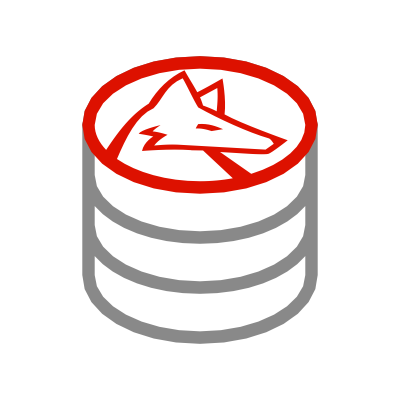

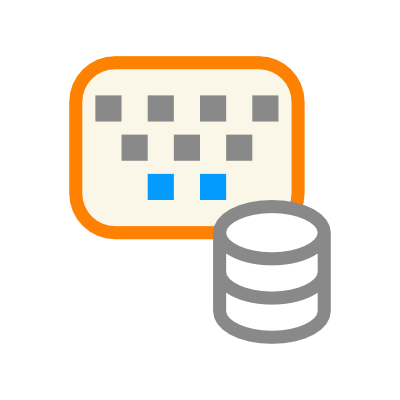

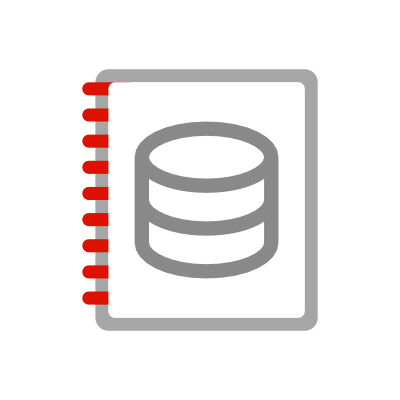

CreateDirectory::enoent: File or directory not found.

Export::nodir: Directory H:\Datenerhebung und Auswertung\ does not exist.

$Failed

```mathematica
transl=.
transl={"variable","date","time","name","atmospheric pressure","temperature","humidity","height above German reference surface","tidal volume","breathing frequency","expiratory reserve volume","inspiratory vital capacity","expiratory vital capacity","forced expiratory volume 1 sec","forced vital capacity","peak expiratory flow","maximal (mid-)expiratory flow 25%","maximal (mid-)expiratory flow 50%","maximal (mid-)expiratory flow 75%","residual volume","total lung capacity","alveolar volume","functional residual capacity","haemoglobin","inspiratory concentration helium","expiratory concentration helium","inspiratory concentration carbon monoxide","expiratory concentration carbon monoxide","diffusion capacitance carbon monoxide"};

exportlist=.
exportlist={{"ID","age","height","sex","dlco","tlco","kcosi","kcotr","inspiratory_concentration_helium","expiratory_concentration_helium","inspiratory_concentration_carbon_monoxide","expiratory_concentration_carbon_monoxide","va","ethnic","fev1","fvc","maximal_(mid-)expiratory_flow_25%","fef2575","fef75","fev075","peak_expiratory_flow","frc","tlc","rv","erv","ic","expiratory_vital_capacity","vc","tidal_volume","breathing_rate_1/min","atmospheric_pressure","temperature","humidity","height_above_German_reference_surface"}};

Map[
(respData=.;
respData=Import[#[[3]]];
respData=StringSplit[Flatten@respData[[15;;Length@respData]],"  "]/.""->Nothing;
respData[[All,1]]=StringReplace[#,{DigitCharacter->"",".94"->"oe"}]&/@respData[[All,1]];
respData[[1]]=Prepend[respData[[1]],"Variable"];
respData=StringReplace[#," "->""]&/@respData;
respData[[All,1]]=transl;
(*TableForm[respData]*)

varProb=.;
varProb=Import[#[[2]]];
varProb=Flatten[StringCases[varProb,#]&/@{"Geschlecht--" ~~Shortest[a__]~~","->a,"Geburtsjahr--" ~~Shortest[a__]~~","->a,"Groesse--" ~~Shortest[a__]~~","->a}];
varProb=varProb/.{"maennlich"->"M","weiblich"->"F","divers"->"M"};
varProb[[2]]=2023-ToExpression[varProb[[2]]];
varProb;

AppendTo[exportlist,varProb[[{2,3,1}]]];
(*
TableForm[Transpose[Prepend[{respData},Table[i,{i,Length@respData}]]]]
*)

PrependTo[exportlist[[-1]],StringCases[respData[[4,2]],DigitCharacter..][[1]]]; (*ID*)


AppendTo[exportlist[[-1]],{"",respData[[-1,4]],"","",respData[[25,4]],respData[[26,4]],respData[[27,4]],respData[[28,4]],respData[[22,4]],0,respData[[14,4]],respData[[15,4]],respData[[17,4]],respData[[18,4]],respData[[19,4]],"",respData[[16,4]],respData[[23,4]],respData[[21,4]],respData[[20,4]],respData[[11,4]],respData[[12,4]],respData[[13,4]],"",Min[ToExpression/@respData[[9,-3;;-1]]] (*Slow Vital Capacity != tidal volume*),Min[ToExpression/@respData[[10,-3;;-1]]] ,StringCases[respData[[5,2]],DigitCharacter..][[1]],
StringCases[respData[[6,2]],DigitCharacter..][[1]],
StringCases[respData[[7,2]],DigitCharacter..][[1]],
StringCases[respData[[8,2]],DigitCharacter..][[1]]
}];
exportlist=Map[Flatten[#]&,exportlist,{1}];

)&,evalfiles];
Export["H:\\Datenerhebung und Auswertung\\lung function testing.xlsx",exportlist]
```

## Upload on http://gli-calculator.ersnet.org/index.html for explanation see http://gli-calculator.ersnet.org/docs.html

```mathematica
replList=.
fn=.
fn=Import["H:\\Projekte\\Quantifizierung humane Aerosolemission\\Datenerhebung und Auswertung\\full names GLI variables.xlsx"];
replList=(#[[1]]->#[[2]])&/@Partition[Flatten@fn,2];

(*
idList=.
idList=StringReplace[Flatten[StringCases[evalfiles[[All,3]],"\\"~~NumberString ..~~"\\"]],"\\"->""];
PrependTo[idList,"ID"];
*)

respData=.
respData=Import["H:\\Projekte\\Quantifizierung humane Aerosolemission\\Datenerhebung und Auswertung\\lung function testing_GLI.xlsx"][[1]];

(*
respData=Map[Flatten[#]&,Transpose[{idList,respData}],{1}];
*)


z=0;
delList=.
delList=Map[(z=z+1;If[Union[#[[2;;-1]]]=={0},z,Nothing])&,Transpose@respData];
 (*lösche Spalten mit 0*)

respData=Transpose@Delete[Transpose@respData,{#}&/@delList];
respData[[1]]=respData[[1]]/.replList;


cvTOvcMale=.
cvTOvcMale[age_Real]:=Module[{},{0.562+0.357 *age,"±2 SEE:",4.15}] (*Closing Volume as % of vital capacity  with 2 Standrad Deviations*)
cvTOvcFemale=.
cvTOvcFemale[age_Real]:=Module[{},{2.812+0.293 *age,"±2 SEE:",4.90}]
(* the closing volume is the endexpiratory volume before total expiration. the here calculated volume is the volume, where no bronchiole closing occurs (the non-closing-volume)  *)
closingVolume=.
closingVolume[l_List]:=Module[{f},If[l[[4]]=="M",f=cvTOvcMale,f=cvTOvcFemale];{f[l[[2]]],{(1-(f[l[[2]]][[1]]/100))*l[[22]],f[l[[2]]][[-1]]*l[[22]]/100}}]

cvList=Transpose[closingVolume/@Rest@respData];
PrependTo[cvList[[1]],"closing volume as percent of vital capacity with 2 Std Dev [from Buis & Ross: Predicted Values for Closing Volumes(...). Amer Rev of Resp Dis 1973]"];
PrependTo[cvList[[2]],"vital capacity - closing volume with 2 Std Dev [from Buis & Ross: Predicted Values for Closing Volumes(...). Amer Rev of Resp Dis 1973]"];

respData=Join[Transpose@respData,cvList];

respDataXLSX=respData;
respDataXLSX[[-2]][[2;;-1]]=StringJoin[ToString@#[[1]]~~" ± "~~ToString@#[[-1]]]&/@Rest@respDataXLSX[[-2]];
respDataXLSX[[-1]][[2;;-1]]=StringJoin[ToString@#[[1]]~~" ± "~~ToString@#[[-1]]]&/@Rest@respDataXLSX[[-1]];

Export[outp~~"lung function testing with GLI references.xlsx",Transpose@respDataXLSX]

Export[outp~~"lung function testing with GLI references.m",Transpose@respData]
```

H:\Projekte\Quantifizierung humane Aerosolemission\Datenerhebung und Auswertung\lung function testing with GLI references.xlsx

H:\Projekte\Quantifizierung humane Aerosolemission\Datenerhebung und Auswertung\lung function testing with GLI references.m

```mathematica
test=.
test=Rest[Select[Transpose[respData],StringContainsQ[#[[1]],"Alveolar Volume Percent Predicted"]&][[1]]];
FindDistribution@test
CDF[FindDistribution@test]
```

$Aborted

Function[x,1/2 Erfc[0.059941 (92.2602-x)]]

```mathematica
data=.
data=Select[Transpose[respData],StringContainsQ[#[[1]],"Percent Predicted"]&]
```

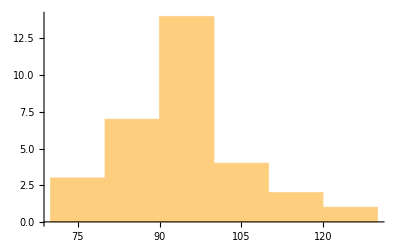
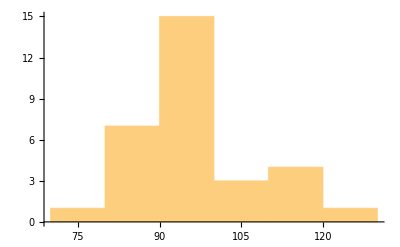
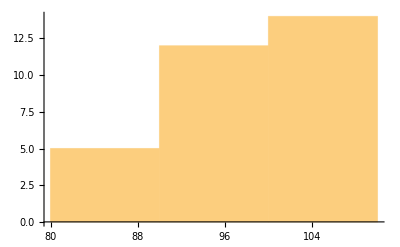
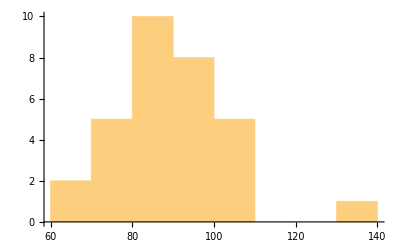
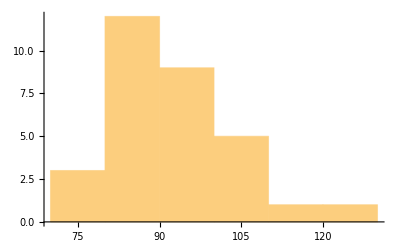
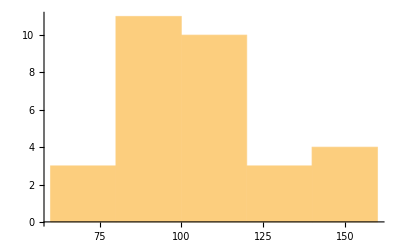
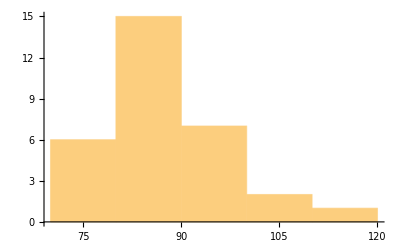
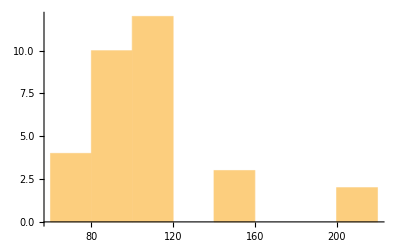
-Graphics- | FEV1 Percent Predicted
-Graphics- | FVC Percent Predicted
-Graphics- | FEV1/FVC Percent Predicted
-Graphics- | TLCO Percent Predicted
-Graphics- | Alveolar Volume Percent Predicted
-Graphics- | FRC Percent Predicted
-Graphics- | TLC Percent Predicted
-Graphics- | RV Percent Predicted
-Graphics- | RVTLC Percent Predicted
-Graphics- | ERV Percent Predicted
-Graphics- | IC Percent Predicted

```mathematica
TableForm@Transpose@{Histogram/@Rest/@data,data[[All,1]]}
```

```mathematica
respData
```